```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/niels/Projects/Johannes

```mathematica
ℏc=197.32858;
Mnucl=(938.2796+939.5731)/2.;
multiplicity=1;
parity="-";
J=0.5;
k=2;
```

```mathematica
litpath3He="/home/kirscher/kette_repo/ComptonLIT/mul_helion_64/";
NormHamMat=ReadList[litpath3He<>"lit_bas_lhs/norm-ham-litME-"<>ToString[J]<>"^"<>parity,Number];
JbasisDim=NormHamMat[[1]];
```

```mathematica
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
```

```mathematica
file=litpath3He<>"LIT_SOURCE_"<>ToString[J]<>"^"<>parity<>"_mJ"<>ToString[J]<>"_MUL"<>ToString[multiplicity];
inhomo=ReadList[file,Real,RecordLists->True];
```

```mathematica
Grid[{{"EV(⟨i|j⟩)\n","EV(⟨i|H_nucl|j⟩)","⟨i|E1(k)|He⟩"},{Eigenvalues[norm]//MatrixForm,Eigenvalues[ham]//MatrixForm,inhomo[[k]]//MatrixForm}}]
```

EV(⟨i|j⟩)
 | EV(⟨i|H_nucl|j⟩) | ⟨i|E1(k)|He⟩
(1.46545×10^6
22702.5
4527.
991.714
490.019
271.631
53.1687
30.9211
8.92677
2.66267
1.47136
1.00498
0.23715
0.081393
0.0106035
0.00709318
0.0024384
0.000391483
0.0000945173
2.88139×10^-6) | (4.84792×10^6
344612.
61949.5
20957.5
13588.6
6813.96
1643.53
1068.78
320.379
121.767
65.276
39.349
11.407
4.05974
0.745763
0.428627
0.151568
0.0284268
0.00627065
0.00018842) | (0.
0.
0.
1.0207
0.15617
0.16141
0.3979
0.19794
0.19228
0.072355
0.064275
0.037193
0.036194
0.051806
0.048291
0.020368
0.031416
0.025096
0.093733
0.16754)

## An unstable test case

What we are trying to solve: the operator equation (ℋ-σ ℐ)|ϕ⟩=|ψ⟩; σ=σ_R+ⅈ σ_I; the result (lit transform) is given by ℒ=⟨ϕ|ϕ⟩. We now decompose |ϕ⟩ and |ψ⟩  in the same nonorthogonal basis |i⟩.
Define N_ij=⟨i|j⟩, H_ij=⟨i|ℋ|j⟩, |ψ⟩=ψ_i|i⟩, |ϕ⟩=ϕ_i|i⟩. Now solve the equation for ϕ,
(H_ij-σ N_ij)ϕ_i=ψ_i, and calculate ℒ=⟨ϕ|ϕ⟩=ϕ_i N_ij ϕ_j

```mathematica
σI=5;
σRmin=-10.;σRmax=100.;σRstep=1;
σR=Range[σRmin,σRmax,σRstep];
litOfSigma={};litOfSigmaNaive={};
psilitOfSigma={};psilitOfSigmaNaive={};
```

```mathematica
ltsσ=Function[{σR},(*{psilitOfSigmaNaive,litOfSigmaNaive,psilitOfSigma,litOfSigma}*)
Block[{coeff},{coeff=Inverse[ham-(σR-σI I) norm].inhomo[[k]],Conjugate[coeff].norm.coeff,coeff=LinearSolve[ham-Conjugate[σR+σI I] norm,inhomo[[k]]],Conjugate[coeff].norm.coeff}]
];
```

```mathematica
{psilitOfSigmaNaive,litOfSigmaNaive,psilitOfSigma,litOfSigma}=Transpose[ltsσ/@σR]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.9356×10^7+7.28767×10^6 ⅈ,1.40117×10^6+464755. ⅈ,736445.+238668. ⅈ,157373.+59700.7 ⅈ,15185.+4708.71 ⅈ,17717.4+5574.4 ⅈ,34241.5+12298.5 ⅈ,17554.4+5638.37 ⅈ,«5»,21607.7+7248.45 ⅈ,117329.+39514.5 ⅈ,10562.6+3236.65 ⅈ,18940.7+6034.81 ⅈ,13972.5+4352. ⅈ,68639.3+21704.9 ⅈ,138919.+45062.3 ⅈ},«18»,{138919.+«17» ⅈ,«18»,«1»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.9356×10^7+7.28767×10^6 ⅈ,1.40117×10^6+464755. ⅈ,736445.+238668. ⅈ,157373.+59700.7 ⅈ,15185.+4708.71 ⅈ,17717.4+5574.4 ⅈ,34241.5+12298.5 ⅈ,17554.4+5638.37 ⅈ,«5»,21607.7+7248.45 ⅈ,117329.+39514.5 ⅈ,10562.6+3236.65 ⅈ,18940.7+6034.81 ⅈ,13972.5+4352. ⅈ,68639.3+21704.9 ⅈ,138919.+45062.3 ⅈ},«18»,{138919.+«17» ⅈ,«18»,«1»}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{1.78985×10^7+7.28767×10^6 ⅈ,1.30822×10^6+464755. ⅈ,688712.+238668. ⅈ,145433.+59700.7 ⅈ,14243.3+4708.71 ⅈ,16602.5+5574.4 ⅈ,31781.8+12298.5 ⅈ,16426.8+5638.37 ⅈ,«5»,20158.+7248.45 ⅈ,109426.+39514.5 ⅈ,9915.24+3236.65 ⅈ,17733.7+6034.81 ⅈ,13102.1+4352. ⅈ,64298.3+21704.9 ⅈ,129907.+45062.3 ⅈ},«18»,{129907.+«1»,«19»}} may contain significant numerical errors.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.78985×10^7+7.28767×10^6 ⅈ,1.30822×10^6+464755. ⅈ,688712.+238668. ⅈ,145433.+59700.7 ⅈ,14243.3+4708.71 ⅈ,16602.5+5574.4 ⅈ,31781.8+12298.5 ⅈ,16426.8+5638.37 ⅈ,«5»,20158.+7248.45 ⅈ,109426.+39514.5 ⅈ,9915.24+3236.65 ⅈ,17733.7+6034.81 ⅈ,13102.1+4352. ⅈ,64298.3+21704.9 ⅈ,129907.+45062.3 ⅈ},«18»,{129907.+«1»,«19»}} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {«1»} may contain significant numerical errors.

General::stop: Further output of LinearSolve::luc will be suppressed during this calculation.

{1}
 |  |  |  |

```mathematica
naive=ListPlot[{Re[litOfSigma],Re[litOfSigmaNaive]},AxesLabel->{"σ_real","a_j𝟙_jia_i ∝ Lit"},PlotLabels->{"mm function","naive"},ImageSize->Large,DataRange->{σRmin,σRmax}]
```

-Graphics-

## A stabilization attempt via singular-value decomposition

Here we tackle the full matrix. Disadvantage of that can be is a separate inverse for each σ; no communality between the truncations at different σ. 
This relies on a pseudo inverse

M=U S A^† with S=diag and U=U^T and A=A^T (both orthogonal as M is square)
S_ii=√(ev_i(M^T M))

```mathematica
reduce[threshold_,σR_]:=Block[{Mm=ham-(σR-σI ⅈ) norm,USA,dimred},USA=SingularValueDecomposition[Mm];dimred=Count[Diagonal[USA[[2]]],u_/;Abs[u]>threshold];{Utrunc,Strunc,Atrunc}={USA[[1]][[All,1;;dimred]],USA[[2]][[1;;dimred,1;;dimred]],USA[[3]][[All,1;;dimred]]}];
```

```mathematica
thresh=10^-1;
mats={norm,ham,ham-Conjugate[σR[[n]]+σI I] norm};
Mm=mats[[3]];
USA=SingularValueDecomposition[Mm];
dimred=Count[Diagonal[USA[[2]]],u_/;Abs[u]>thresh]
Utrunc=USA[[1]][[All,1;;dimred]];
Strunc=USA[[2]][[1;;dimred,1;;dimred]];
Atrunc=USA[[3]][[All,1;;dimred]];
Mmapprox=Utrunc.Strunc.ConjugateTranspose[Atrunc];
Mmtrunc=ConjugateTranspose[Utrunc].Mm.Utrunc;

Grid[{{"EV(M_L_2)","EV(O_range^t·M·O_range)","EV(M)"},{Eigenvalues[Mmapprox]//MatrixForm,Eigenvalues[Mmtrunc]//MatrixForm,Eigenvalues[Mm]//MatrixForm}}]
```

Part::pkspec1: The expression n cannot be used as a part specification.

$Aborted

Part::partd: Part specification USA⟦2⟧ is longer than depth of object.

Diagonal::list: List expected at position 1 in Diagonal[USA⟦2⟧].

0

Part::partd: Part specification USA⟦1⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::pkspec1: The expression Integer[] cannot be used as a part specification.

Part::partd: Part specification USA⟦2⟧ is longer than depth of object.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

Part::partd: Part specification USA⟦3⟧ is longer than depth of object.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::pkspec1: The expression Integer[] cannot be used as a part specification.

$Aborted

### reduced-basis (Niels vs. Penrose pseudo inverse)

Here we tackle the full matrix. Disadvantage of that can be is a separate inverse for each σ; no communality between the truncations at different σ. 
This relies on a pseudo inverse

Use M_ij=(H_ij-σ N_ij).
Write the SVD M=U S A^† with S=diag and U=U^T and A=A^T (both orthogonal as M is square)
S_ii=√(ev_i(M^T M)). We can  now define a pseudo inverse by
M^-1=A P S^-1 P U^†, where P  projects on sensible values  of S (greater than a threshold t)

There is an alternative
(H_ij-σ N_ij)ϕ_i=ψ_i. Diagonalise N, N_ij O_jn=μ^(n)O_in, call the eigenvalues μ. Define (ϕ̃)_j=N_ji^(1/2)ϕ_i, where N_ji^x=O_bj μ_b^x O_bi^We then solve
(N_ki^(-1/2)H_ij N_lj^(-1/2)-σ )(ϕ̃)_l=N_li^(-1/2)ψ_i. Again, the subset of indices b is defined by a truncation, μ^(n)>t. The Lit is now ℒ=⟨ϕ|ϕ⟩=(ϕ̃)_l(ϕ̃)_l.
This becomes even nicer in terms of the eigenvalues of (H̃)_ab=μ_a^(-1/2) O_ai H_ij O_bj μ_b^(-1/2); Writing (H̃)_ab e_b^(m)=λ^(m)e_a^(m), and (ψ̃)^(m)=∑_a e_a^(m)μ_a^(-1/2) O_ai ψ_i, we have ℒ=⟨ϕ|ϕ⟩=∑_m (|(ψ̃)^(m)|^2)/(|λ^(m)-σ|^2)

```mathematica
pseudoinverse[threshold_,σR_,σI_]:=Block[{Mm=ham-(σR-σI ⅈ) norm,USA,dimred},PseudoInverse[Mm,Tolerance->threshold]]
```

```mathematica
normreg[threshold_]:=Block[{es=Eigensystem[norm],μ,transf},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])]
```

```mathematica
decompose[threshold_]:= Block[{Oμ=normreg[threshold],oλs,otrf},{λs,trf}=Eigensystem[(Transpose[Oμ].ham).Oμ];{λs,trf.(Transpose[Oμ].inhomo[[k]])}]
```

```mathematica
litcomp[threshold_]:=Block[{λscf=Transpose[decompose[threshold]]},Plus@@(((#[[2]])^2/((#[[1]]-σRe)^2+σIm^2))&/@λscf)]
```

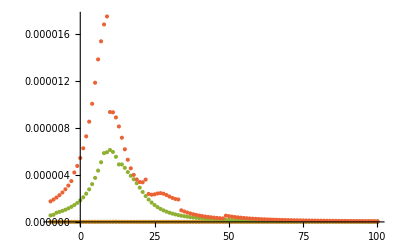

```mathematica
ListPlot[(Function[{σR},Block[{mm,coeff},mm=pseudoinverse[#,σR,σI];coeff=mm.inhomo[[k]];{σR,Chop[Conjugate[coeff].norm.coeff]}]]/@σR)&/@{10^-1,10^-2,10^-3,10^-4},PlotRange->All]
```

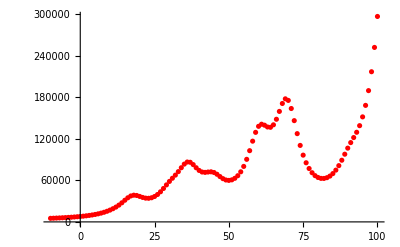

```mathematica
alt=ListPlot[Function[{σR},Block[{mm,coeff},mm=pseudoinverse[10^-18,σR,σI];coeff=mm.inhomo[[k]];{σR,Re[Conjugate[coeff].norm.coeff]}]]/@σR,PlotRange->All,PlotStyle->Red]
```

```mathematica
Show[f=litcomp[10^-20]/.σIm->σI;Plot[f,{σRe,-10,100}],naive,alt]
```

-Graphics-

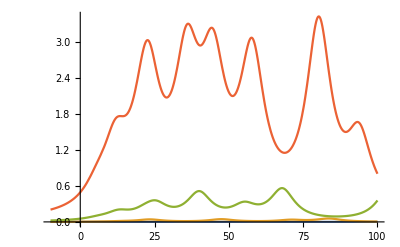

```mathematica
Plot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@{0.1,0.001,0.0001,0.00001})],{σRe,-10,100}]
```

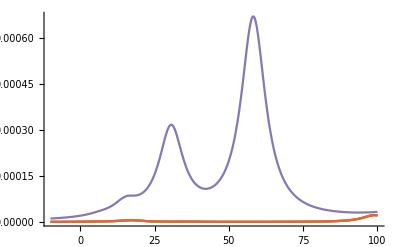

```mathematica
Plot[Evaluate[((f=litcomp[#]/.σIm->σI)&/@{1,0.8,0.6,0.4,0.2})],{σRe,-10,100},PlotRange->All]
```